```mathematica
SetDirectory[NotebookDirectory[]]
pblue=Lighter[Blue];
pyellow=Lighter[Yellow];
pred=Lighter[Red];
pgreen=Lighter[Green];
cf=Piecewise[{{Blend[{pred,pblue},(#+Pi)/(Pi/2)],#≤-Pi/2},{Blend[{pblue,pgreen},(#+Pi/2)/(Pi/2)],#≤0},{Blend[{pgreen,pyellow},(#)/(Pi/2)],#≤Pi/2},{Blend[{pyellow,pred},(#-Pi/2)/(Pi/2)],#≤Pi}}]&;
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]]
phase[l:{_?NumericQ..}]:=Module[{args=Arg[l]},args+Prepend[2Pi Accumulate@-IntegerPart@Differences[args/Pi],0]]
nmax=10;
getphase[sig_]:=Module[{asig,plst,S1,slst1,f1},
asig=Fourier[ReplacePart[InverseFourier[sig-Mean[sig]],Join[{{1}},{#}&/@(Floor[Length[sig]/2]+Range[Floor[Length[sig]/2]])]->0]];
plst=phase[asig];
S1[n_]:=Sum[Exp[-I*n*plst[[i]]], {i,1,Length[plst]}]/Length[plst];
slst1=Table[S1[n]/(I*n),{n,1,nmax}];
f1[θ_]:=θ+Evaluate[Sum[2*Re[slst1][[n]]*(Cos[n*θ]-1)-2*Im[slst1][[n]]*Sin[n*θ],{n,1,nmax}]];
f1/@plst]
```

/home/zack/Desktop/snakingoscillators

#### Single trajectory runs

-Graphics-

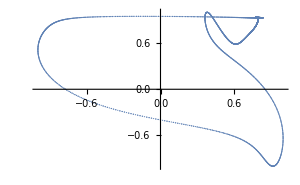
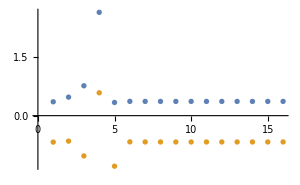
i | 1503 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
filebase="data/test";
dat=BinaryReadList[filebase<>"phases.npy","Real64"][[17;;-1]];
M=16;
theta=ArcTan[Partition[dat,4*M][[All,1;;M]],Partition[dat,4*M][[All,M+1;;2*M]]];
phi=ArcTan[Partition[dat,4*M][[All,2*M+1;;3*M]],Partition[dat,4*M][[All,3*M+1;;4*M]]];
rasterizeBackground[ListDensityPlot[theta,AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]]
phases=Transpose[Catenate[{Transpose[theta],Transpose[phi]}]];
dphases=(#-#[[1]]&/@phases);
norms=Norm[#-dphases[[-1]]]&/@dphases;
mins=First/@Position[Differences[Sign[Differences[norms]]],u_/;u>0];
periods=Differences[Cases[mins,u_/;norms[[u]]<1]];
If[Length[periods]>0,
period=Round[Mean[periods]];
Grid[{{i,period,rasterizeBackground[ListDensityPlot[theta[[1;;period]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListDensityPlot[phi[[1;;period]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],ListPlot[Transpose[{Cos[phi[[All,1]]],Cos[theta[[All,1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300],ListPlot[{theta[[-1]],phi[[-1]]},ImageSize->300]}}]]
```

```mathematica
orders=BinaryReadList[filebase<>"order.npy","Real64"][[17;;-1]];
Mean[orders[[-period;;-1]]]
Norm[Transpose[Transpose[dphases[[-period+1;;-1]]]-dphases[[-1]]],2]
```

0.773607

126.436

#### Chimeras from random initial conditions

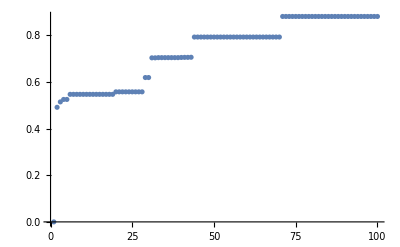

{{1.00197×10^-16,13},{0.491492,35},{0.514692,8},{0.525224,64},{0.5471,12},{0.55779,43},{0.61917,2},{0.70364,52},{0.792873,59},{0.881127,6}}

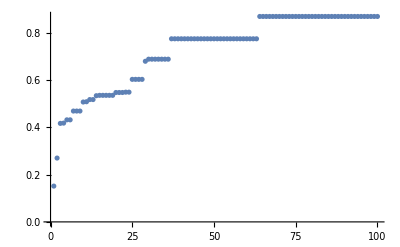

{{0.151251,93},{0.269736,8},{0.416212,18},{0.417372,60},{0.431174,83},{0.468339,62},{0.50651,43},{0.507694,70},{0.516818,67},{0.533197,82},{0.534698,26},{0.546692,31},{0.548146,98},{0.602216,73},{0.678699,59},{0.687495,1},{0.773606,3},{0.867984,16}}

```mathematica
orders=Table[Import["data/random/"<>ToString[i]<>"out.dat"][[2,2]],{i,1,100}];
ListPlot[Sort[orders]]
uniq=Join[{1},1+First/@Position[Differences[Sort[orders]],u_/;Abs[u]>10^-3]];
Transpose[{Sort[orders][[uniq]],Ordering[orders][[uniq]]}]

orders2=Table[Import["data/random2/"<>ToString[i]<>"out.dat"][[2,2]],{i,1,100}];
ListPlot[Sort[orders2]]
uniq2=Join[{1},1+First/@Position[Differences[Sort[orders2]],u_/;Abs[u]>10^-3]];
Transpose[{Sort[orders2][[uniq2]],Ordering[orders2][[uniq2]]}]
```

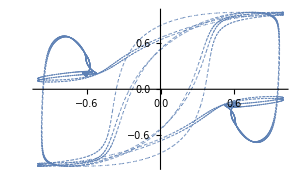
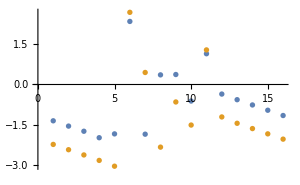
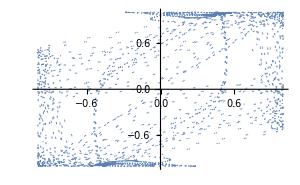
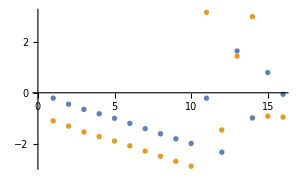
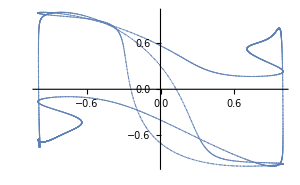
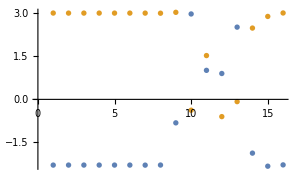
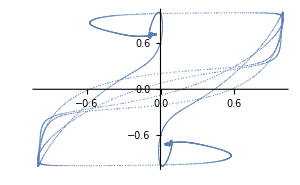
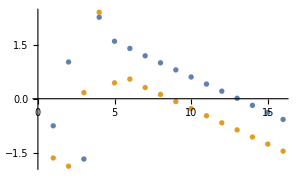
343 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
798 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
167 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
335 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
304 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
1083 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
174 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
172 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
p=Grid[Table[filebase="data/random/"<>ToString[i];
dat=BinaryReadList[filebase<>"phases.npy","Real64"][[17;;-1]];
M=16;
theta=ArcTan[Partition[dat,4*M][[All,1;;M]],Partition[dat,4*M][[All,M+1;;2*M]]];
phi=ArcTan[Partition[dat,4*M][[All,2*M+1;;3*M]],Partition[dat,4*M][[All,3*M+1;;4*M]]];
dthetas=(#-#[[1]]&/@theta);
norms=Norm[#-dphases[[1]]]&/@dphases;
mins=First/@Position[Differences[Sign[Differences[norms]]],u_/;u>0];
periods=Differences[Cases[mins,u_/;norms[[u]]<1]];
{Grid[{{period,rasterizeBackground[ListDensityPlot[theta[[1;;period]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListDensityPlot[phi[[1;;period]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],ListPlot[Transpose[{Cos[phi[[All,1]]],Cos[theta[[All,1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300],ListPlot[{theta[[-1]],phi[[-1]]},ImageSize->300]}}]},{i,Ordering[orders][[uniq[[2;;-2]]]]}]]
```

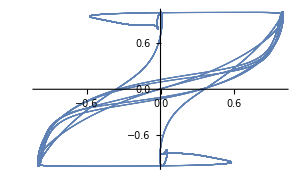
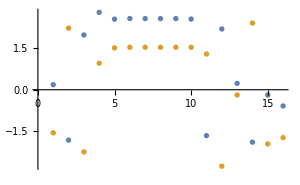
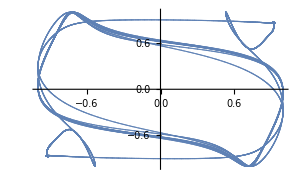
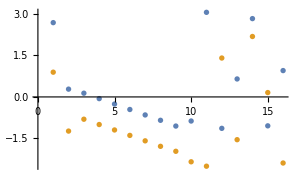
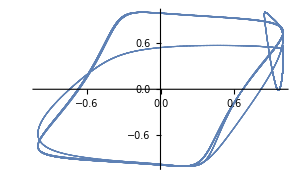
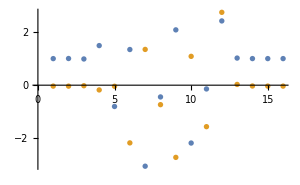
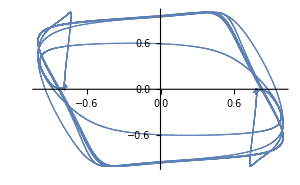
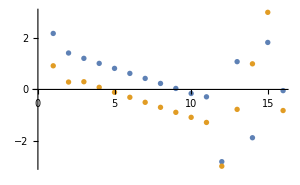
1 | 2194 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
3 | 2970 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
4 | 1486 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
5 | 2970 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
6 | 3017 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
7 | 2970 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
8 | 5946 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
9 | 3012 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
10 | 2968 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
11 | 2836 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
12 | 2812 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
13 | 1487 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
14 | 1503 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
15 | 1487 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
16 | 1503 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Monitor[p=Grid[DeleteCases[Table[filebase="data/chimera/"<>ToString[j];
dat=BinaryReadList[filebase<>"phases.npy","Real64"][[17;;-1]];
M=16;
theta=ArcTan[Partition[dat,4*M][[All,1;;M]],Partition[dat,4*M][[All,M+1;;2*M]]];
phi=ArcTan[Partition[dat,4*M][[All,2*M+1;;3*M]],Partition[dat,4*M][[All,3*M+1;;4*M]]];
phases=Transpose[Catenate[{Transpose[theta],Transpose[phi]}]];
dphases=(#-#[[1]]&/@phases);
norms=Norm[#-dphases[[1]]]&/@dphases;
mins=First/@Position[Differences[Sign[Differences[norms]]],u_/;u>0];
periods=Differences[Cases[mins,u_/;norms[[u]]<1]];
If[Length[periods]>0,
period=Round[Mean[periods]];
states=Table[Flatten[{0.1*(i-Length[dphases]+period),Cos[dphases[[i,2;;16]]],Sin[dphases[[i,2;;16]]],Cos[dphases[[i,17;;32]]],Sin[dphases[[i,17;;32]]]}],{i,Length[dphases]-period+1,Length[dphases]}];
Export["data/chimera_rel_"<>ToString[j]<>".dat",states];
{Grid[{{j,period,rasterizeBackground[ListDensityPlot[theta[[1;;period]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListDensityPlot[phi[[1;;period]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],ListPlot[Transpose[{Cos[phi[[All,1]]],Cos[theta[[All,1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300],ListPlot[{theta[[-1]],phi[[-1]]},ImageSize->300]}}]}],{j,1,16}],Null]],{j,period}]
```

#### Plot auto results

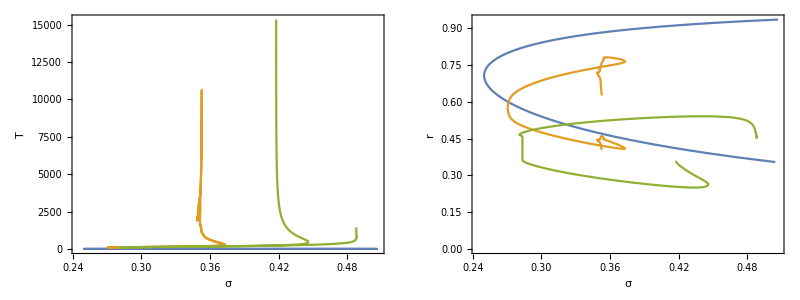

```mathematica
Grid[{{ListPlot[{Import["auto/rel/janus_rels.dat"][[1;;-2,{1,7}]],Import["auto/rel/janus_rel1.dat"][[1;;-2,{1,7}]],Import["auto/rel/janus_rel2.dat"][[1;;-2,{1,7}]]},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,T},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1],ListPlot[{Import["auto/rel/janus_rels.dat"][[1;;-2,{1,8}]],Import["auto/rel/janus_rel1.dat"][[1;;-2,{1,8}]],Import["auto/rel/janus_rel2.dat"][[1;;-2,{1,8}]]},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1]}}]
```